```mathematica
generateKeyWithPlot[seed_Integer,tBurn_:1]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,traj1,traj2,traj3,timeSteps,positions,keyData,binaryKeyData,key,initialPoints,trajectoryPlot},(*Initial conditions*)pos1={0,0};
vel1={0,10}*conv;
SeedRandom[seed];
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};
(*Differential equations*)eq={x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};
(*Initial conditions for solver*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve system-- still integrated from t=0*)sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];
traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;
(*Sample positions-- skip burn-in[0,tBurn)*)timeSteps=Range[tBurn,100,0.01];
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];
(*Convert to 32-bit binary*)keyData=Flatten[positions];
binaryKeyData=Flatten[Table[IntegerDigits[Floor[Mod[Abs[val]*10^9,2^32]],2,32],{val,keyData}]];
key=Flatten[binaryKeyData];
(*Print info*)Print["Seed: ",seed,"   burn-in t < ",tBurn," (",Round[tBurn/0.01]," steps dropped)"];
Print["Key length: ",Length[key]];
Print["Counts: ",Counts[key]];
(*Plot trajectories-- full run incl.burn-in,for reference*)initialPoints={pos1,pos2,pos3};
trajectoryPlot=ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thin],FrameLabel->{Style["x (au)",Italic,14],Style["y (au)",Italic,14]},PlotRange->{{-10,10},{-5,15}},AspectRatio->1,AxesOrigin->{0,0},ImageSize->500,PlotLegends->Placed[LineLegend[{"Particle 1","Particle 2","Particle 3"},LegendMarkerSize->10,LegendFunction->(Framed[#,RoundingRadius->0]&)],Below],Epilog->{Black,PointSize[Large],Point[initialPoints]}];
Print[trajectoryPlot];
key]
```

Seed: 105   burn-in t < 1 (100 steps dropped)

Key length: 1900992

Counts: <|0→963436,1→937556|>

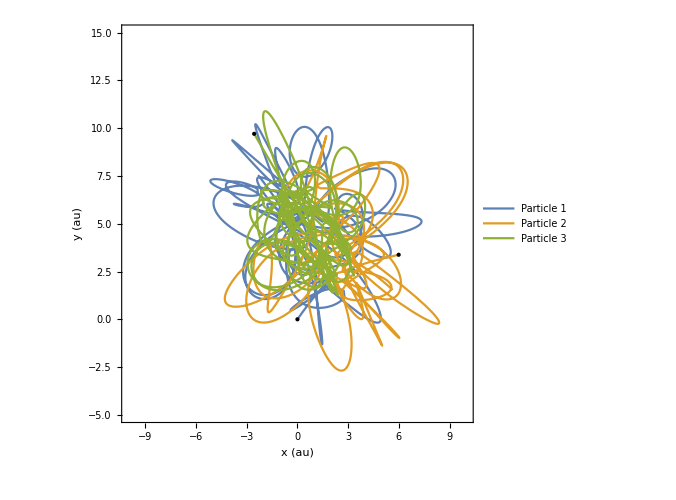

Seed: 121   burn-in t < 1 (100 steps dropped)

Key length: 1900992

Counts: <|0→959233,1→941759|>

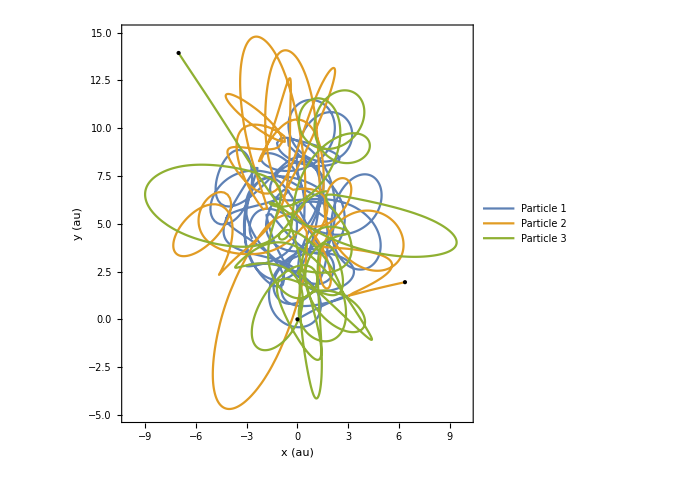

Seed 105 timing: 0.661428 seconds

Seed 121 timing: 0.425899 seconds

XOR key length: 1900992

XOR key counts: <|0→951245,1→949747|>

NotebookDirectory::nosv: The notebook obj is not saved.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File.

```mathematica
seedA=105;seedB=121;tBurn=1;

{time1,key1}=AbsoluteTiming[generateKeyWithPlot[seedA,tBurn]];
{time2,key2}=AbsoluteTiming[generateKeyWithPlot[seedB,tBurn]];

len=Min[Length[key1],Length[key2]];
key=BitXor[key1[[;;len]],key2[[;;len]]];

Print["Seed ",seedA," timing: ",time1," seconds"];
Print["Seed ",seedB," timing: ",time2," seconds"];
Print["XOR key length: ",len];
Print["XOR key counts: ",Counts[key]];

(*Export as ASCII 0/1 for NIST STS-- each key alone and the XOR*)
SetDirectory[NotebookDirectory[]];
Export["key_"<>ToString[seedA]<>".txt",StringJoin[ToString/@key1],"Text"];
Export["key_"<>ToString[seedB]<>".txt",StringJoin[ToString/@key2],"Text"];
Export["key_xor.txt",StringJoin[ToString/@key],"Text"];
```